```mathematica
simulateCasinoGame[g_,t_]:=Module[{money,coinToss,plotData,timeAverage,ensembleAverage,gamblerPlot,averagePlot},(*Initial money for each g*)money=Table[100,{g}];
(*canino game*)plotData=Table[(*gia kathe gambler*)coinToss=RandomChoice[{0.5,0.5}->{1.5,0.6},g];
money=money*coinToss;
money,{t}];
(*plot gia kathe gambler's money me basi to time*)gamblerPlot=ListLinePlot[Transpose[plotData],AxesLabel->{"Number of Tosses","Money"},PlotRange->All,PlotLegends->Automatic];
timeAverage=Mean/@plotData;(*mesos oros gia kathe periodo*)ensembleAverage=0.5*1.5+0.5*0.6;(*Plot time-avg kai ensemble-avg*)averagePlot=ListLinePlot[{timeAverage,ConstantArray[ensembleAverage*100,Length[plotData]]},AxesLabel->{"Number of Tosses","Average Return (%)"},PlotLegends->{"Time Average","Ensemble Average"}];
(*ta results*){gamblerPlot,averagePlot,timeAverage,ensembleAverage}]


simulateCasinoGame[50,500]
```

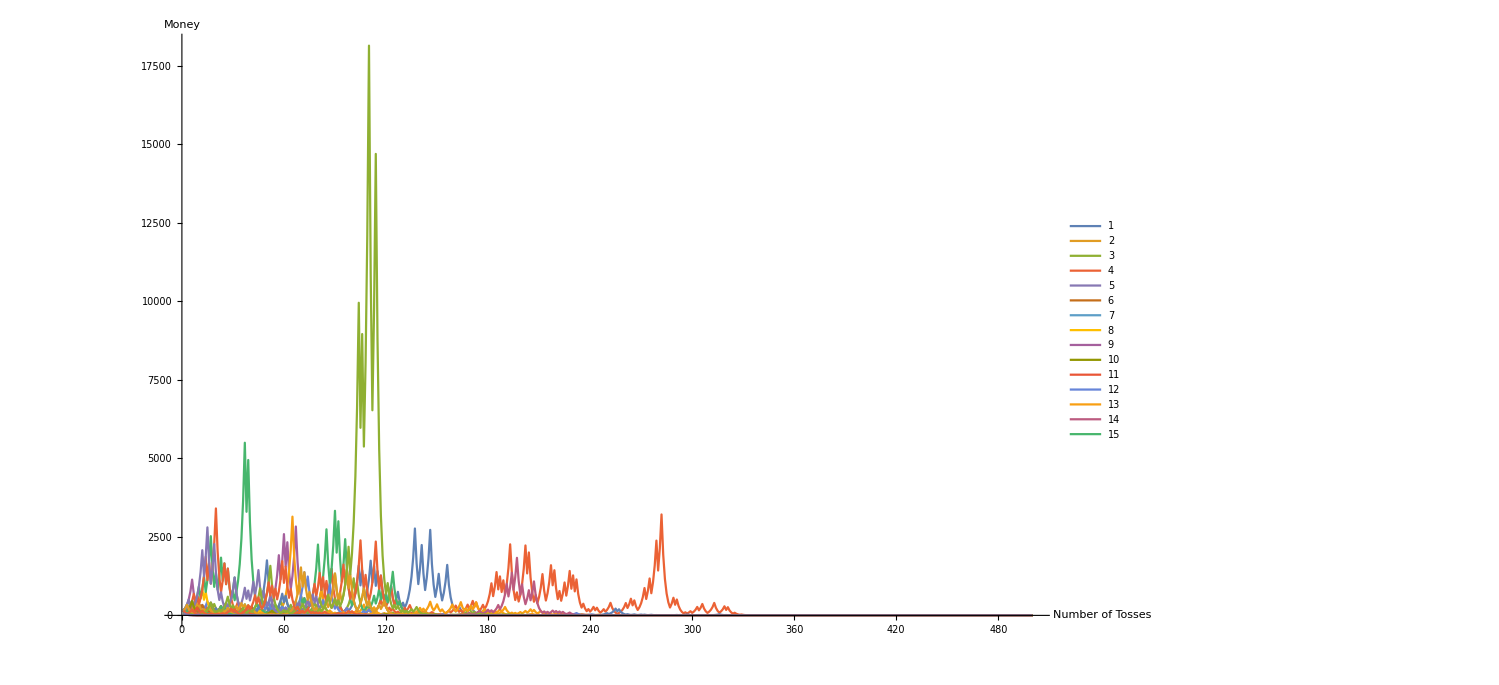
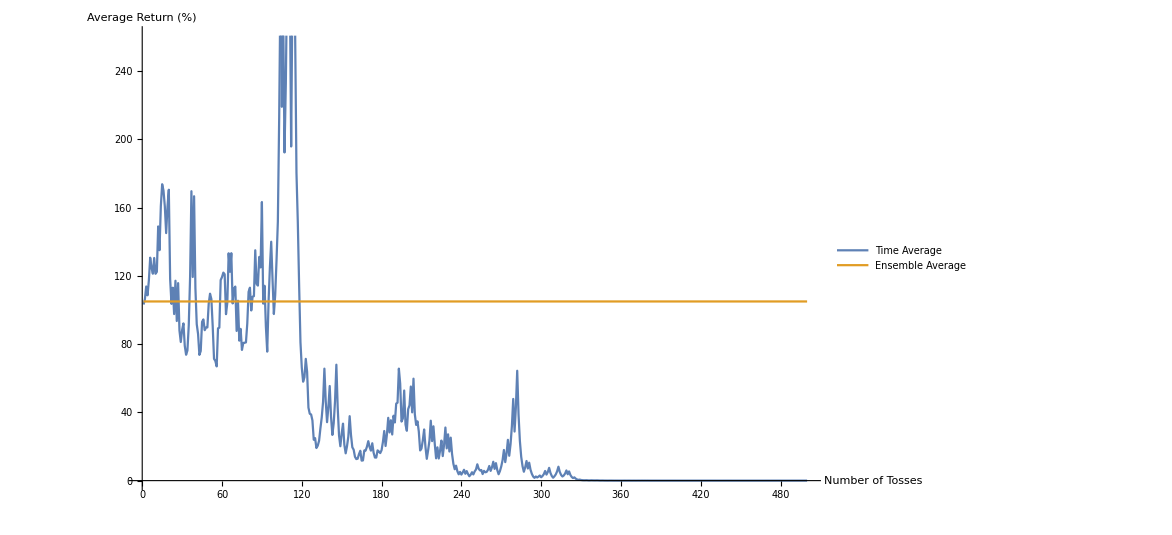

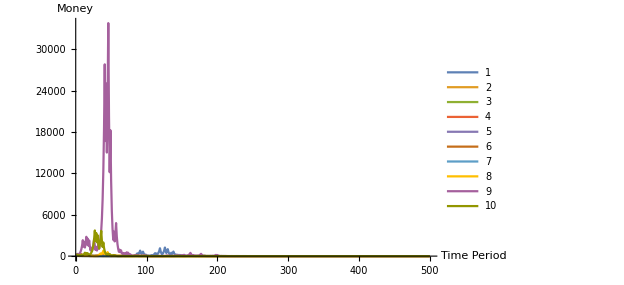
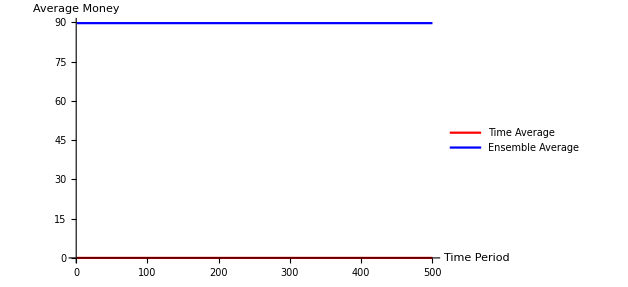
{-Graphics-,-Graphics-,0.0000396933,89.7283}

```mathematica
simulateCasinoBet[g_,t_]:=Module[{money,coinToss,plotData,timeAverage,ensembleAverage,gamblerPlot,averagePlot},(*Initialize money for each gambler*)money=Table[100,{g}];
(*Simulate the betting process*)plotData=Table[coinToss=RandomChoice[{0.5,0.5}->{1.5,0.6},g];
money=money*coinToss;
money,{t}];
(*Create plot for each gambler's money over time*)gamblerPlot=ListLinePlot[Transpose[plotData],AxesLabel->{"Time Period","Money"},PlotRange->All,PlotLegends->Automatic];
(*Calculate time-average return*)timeAverage=Mean[Last[plotData]];
(*Calculate ensemble-average return*)ensembleAverage=Mean[Flatten[plotData]];
(*Plot Time Average and Ensemble Average*)averagePlot=ListLinePlot[{ArrayPad[{timeAverage},{0,t-1},"Fixed"],ArrayPad[{ensembleAverage},{0,t-1},"Fixed"]},AxesLabel->{"Time Period","Average Money"},PlotStyle->{Red,Blue},PlotLegends->{"Time Average","Ensemble Average"}];
(*Return results*){gamblerPlot,averagePlot,timeAverage,ensembleAverage}]

(*Example usage*)
simulateCasinoBet[10,500]
```